(ⅇ^(-y^2) (1-(ⅇ^(-y^2))^m))/(1-ⅇ^(-y^2))

```mathematica
S[y_,m_,n_]:=Module[{phi,x,P0,P1,P2,P3,P4,P5,P6,F1,F2,F3,res1,res2},
phi=Exp[-y^2];
x=2^n-1;
P0=(1/y^4)*(m*y^2-(1-phi^m));
P1=phi*(1-phi^m)/(1-phi);
P1=(1-phi^2/y^2)*(1-phi^m);
P2=(1-(2*phi^m)^n)/(1-2*phi^m);
P3=(phi^m-phi^(2*m*n))/(1-phi^m);
P4=(2*phi^(2m)-(2*phi^m)^(2*n))/(1-2*phi^(2m));
P5=2*phi^(2m)/(1-2*phi^(2m));
P6=1/(1-2*phi^m);
F1 = 6*P1^2*P6*(2^(n-1)-1-2^(n-1)*P3);
F2=3*P1^2*P6*phi^m*(2^n-2-P4)/(1-phi^m);
F3=3*P1^2*P6*P5*(2^(n-1)*(P3/phi^m)-(2*phi^m)^(n-1)*P4);
res1=1+6*P1*P2+6*x*(P0+(P1*P2)^2)
                      +3*P2^2*P6*(3*x-P2+(x+1)*(P5*P2-P3*P4));
res2=1+6*P1*P2+6*(x*P0+(P1*P2)^2)+2*F1+F2-F3;
                      +P1^2*P6*(3*x-P2+(x+1)*(P5*P2-P3*P4));
res2
]
```

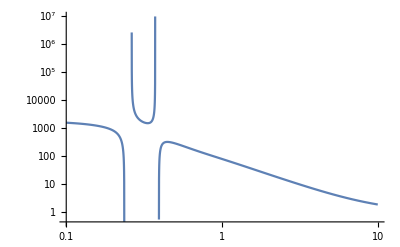

```mathematica
LogLogPlot[{S[y,5,2]},{y,0.1,10}]
```